```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tep/Dropbox/Mon Mac (MBP-de-admin)/Documents/GitHub/Linear-Galactic-Disk-Theory/code/nb

## Eigenvalues

```mathematica
tabEigVals=Import["../data/Dump_Eigenvalues.hf5",{"Datasets","tabEigVals"}];
tabEigValsPhys=Import["../data/Dump_Eigenvalues.hf5",{"Datasets","tabEigValsPhys"}];
tabEigValsReal=tabEigVals[[All,1]];
tabEigValsImag=tabEigVals[[All,2]];
tabEigValsPhysReal=tabEigValsPhys[[All,1]];
tabEigValsPhysImag=tabEigValsPhys[[All,2]];
tabEigValsPlane={tabEigValsReal,tabEigValsImag}//Transpose;
tabEigValsPhysPlane={tabEigValsPhysReal,tabEigValsPhysImag}//Transpose;
```

1

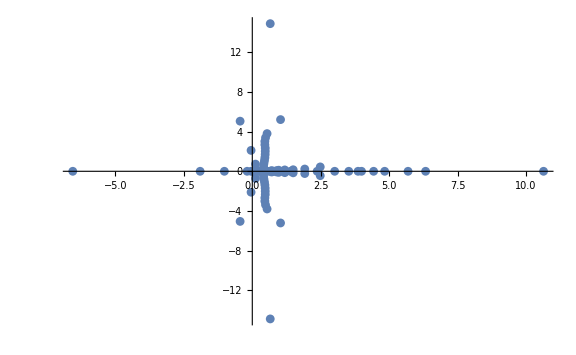

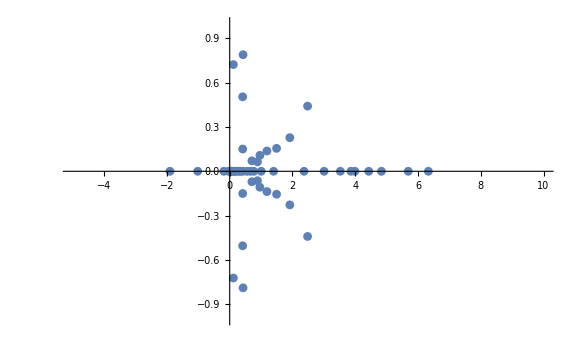

```mathematica
imMax=1
pEig=ListPlot[{tabEigValsPlane},ImageSize->Large,PlotRange->All]
pEig=ListPlot[{tabEigValsPlane},ImageSize->Large,PlotRange->{{-5,10},{-imMax,imMax}}]
```

#### Save data

```mathematica
Export["../graphs/growthRateMathematica.png",pGR]
```

../graphs/growthRateMathematica.png